Enter parameters for 2 ellipses here:

```mathematica
Angle = 20* Pi/180
```

π/9

```mathematica
semiMajor = 5
```

5

```mathematica
semiMinor = 4
```

4

```mathematica
h = 9
```

9

```mathematica
k = 12
```

12

```mathematica
AngleB = 90* Pi/180
```

π/2

```mathematica
semiMajorB = 4
```

4

```mathematica
semiMinorB = 1
```

1

```mathematica
hB = 2
```

2

```mathematica
kB = 15
```

15

Find symmetric matrix for ellipse A:

```mathematica
a11 = (Cos[Angle]/semiMajor)^2 + (Sin[Angle]/semiMinor)^2
```

1/25 Cos[π/9]^2+1/16 Sin[π/9]^2

```mathematica
a12 = (Sin[Angle]*Cos[Angle])/(semiMajor)^2 - (Sin[Angle]*Cos[Angle])/(semiMinor)^2
```

-9/400 Cos[π/9] Sin[π/9]

```mathematica
a21 = a12
```

-9/400 Cos[π/9] Sin[π/9]

```mathematica
a22 = (Sin[Angle]/semiMajor)^2 + (Cos[Angle]/semiMinor)^2
```

1/16 Cos[π/9]^2+1/25 Sin[π/9]^2

```mathematica
a13 = (-Cos[Angle] *( h*Cos[Angle] + k*Sin[Angle] ))/(semiMajor^2 ) + (Sin[Angle] *( k*Cos[Angle] - h*Sin[Angle] ))/(semiMinor^2 )
```

1/16 (12 Cos[π/9]-9 Sin[π/9]) Sin[π/9]-1/25 Cos[π/9] (9 Cos[π/9]+12 Sin[π/9])

```mathematica
a31 = a13
```

1/16 (12 Cos[π/9]-9 Sin[π/9]) Sin[π/9]-1/25 Cos[π/9] (9 Cos[π/9]+12 Sin[π/9])

```mathematica
a23 = (-Sin[Angle] *( h*Cos[Angle] + k*Sin[Angle] ))/(semiMajor^2 ) + (Cos[Angle] *( h*Sin[Angle] - k*Cos[Angle] ))/(semiMinor^2 )
```

1/16 Cos[π/9] (-12 Cos[π/9]+9 Sin[π/9])-1/25 Sin[π/9] (9 Cos[π/9]+12 Sin[π/9])

```mathematica
a32 = a23
```

1/16 Cos[π/9] (-12 Cos[π/9]+9 Sin[π/9])-1/25 Sin[π/9] (9 Cos[π/9]+12 Sin[π/9])

```mathematica
a33 = ((h*Cos[Angle] + k*Sin[Angle])/(semiMajor))^2 + ((h*Sin[Angle] - k*Cos[Angle])/(semiMinor))^2  - 1
```

-1+1/16 (-12 Cos[π/9]+9 Sin[π/9])^2+1/25 (9 Cos[π/9]+12 Sin[π/9])^2

```mathematica
matA={{a11,a12,a13},{a21,a22,a23},{a31,a32,a33}}
```

{{1/25 Cos[π/9]^2+1/16 Sin[π/9]^2,-9/400 Cos[π/9] Sin[π/9],1/16 (12 Cos[π/9]-9 Sin[π/9]) Sin[π/9]-1/25 Cos[π/9] (9 Cos[π/9]+12 Sin[π/9])},{-9/400 Cos[π/9] Sin[π/9],1/16 Cos[π/9]^2+1/25 Sin[π/9]^2,1/16 Cos[π/9] (-12 Cos[π/9]+9 Sin[π/9])-1/25 Sin[π/9] (9 Cos[π/9]+12 Sin[π/9])},{1/16 (12 Cos[π/9]-9 Sin[π/9]) Sin[π/9]-1/25 Cos[π/9] (9 Cos[π/9]+12 Sin[π/9]),1/16 Cos[π/9] (-12 Cos[π/9]+9 Sin[π/9])-1/25 Sin[π/9] (9 Cos[π/9]+12 Sin[π/9]),-1+1/16 (-12 Cos[π/9]+9 Sin[π/9])^2+1/25 (9 Cos[π/9]+12 Sin[π/9])^2}}

```mathematica
MatrixForm[matA]
```

(1/25 Cos[π/9]^2+1/16 Sin[π/9]^2 | -9/400 Cos[π/9] Sin[π/9] | 1/16 (12 Cos[π/9]-9 Sin[π/9]) Sin[π/9]-1/25 Cos[π/9] (9 Cos[π/9]+12 Sin[π/9])
-9/400 Cos[π/9] Sin[π/9] | 1/16 Cos[π/9]^2+1/25 Sin[π/9]^2 | 1/16 Cos[π/9] (-12 Cos[π/9]+9 Sin[π/9])-1/25 Sin[π/9] (9 Cos[π/9]+12 Sin[π/9])
1/16 (12 Cos[π/9]-9 Sin[π/9]) Sin[π/9]-1/25 Cos[π/9] (9 Cos[π/9]+12 Sin[π/9]) | 1/16 Cos[π/9] (-12 Cos[π/9]+9 Sin[π/9])-1/25 Sin[π/9] (9 Cos[π/9]+12 Sin[π/9]) | -1+1/16 (-12 Cos[π/9]+9 Sin[π/9])^2+1/25 (9 Cos[π/9]+12 Sin[π/9])^2)

Find symmetric matrix for ellipse B:

```mathematica
N[matA]
```

{{0.042632,-0.00723136,-0.296912},{-0.00723136,0.059868,-0.653334},{-0.296912,-0.653334,9.51221}}

```mathematica
b11 = (Cos[AngleB]/semiMajorB)^2 + (Sin[AngleB ]/semiMinorB)^2
```

1

```mathematica
b12 = (Sin[AngleB]*Cos[AngleB])/(semiMajorB)^2 - (Sin[AngleB]*Cos[AngleB])/(semiMinorB)^2
```

0

```mathematica
b21 = b12
```

0

```mathematica
b22 = (Sin[AngleB]/semiMajorB)^2 + (Cos[AngleB]/semiMinorB)^2
```

1/16

```mathematica
b13 = (-Cos[AngleB] *( hB*Cos[AngleB] + kB*Sin[AngleB] ))/(semiMajorB^2 ) + (Sin[AngleB] *( kB*Cos[AngleB] - hB*Sin[AngleB] ))/(semiMinorB^2 )
```

-2

```mathematica
b31 = b13
```

-2

```mathematica
b23 = (-Sin[AngleB] *( hB*Cos[AngleB] + kB*Sin[AngleB] ))/(semiMajorB^2 ) + (Cos[AngleB] *( hB*Sin[AngleB] - kB*Cos[AngleB] ))/(semiMinorB^2 )
```

-15/16

```mathematica
b32 =b23
```

-15/16

```mathematica
b33 = ((hB*Cos[AngleB] + kB*Sin[AngleB])/(semiMajorB))^2 + ((hB*Sin[AngleB] - kB*Cos[AngleB])/(semiMinorB))^2  - 1
```

273/16

```mathematica
matB={{b11,b12,b13},{b21,b22,b23},{b31,b32,b33}}
```

{{1,0,-2},{0,1/16,-15/16},{-2,-15/16,273/16}}

Find the characteristic polynomial of the pencil:

```mathematica
MatrixForm[matB]
```

(1 | 0 | -2
0 | 1/16 | -15/16
-2 | -15/16 | 273/16)

```mathematica
N[matB]
```

{{1.,0.,-2.},{0.,0.0625,-0.9375},{-2.,-0.9375,17.0625}}

```mathematica
charPolynomial = Det[λ*matA+ matB]
```

-1/16-λ/16+(593 λ Cos[π/9]^2)/6400-13/200 λ^2 Cos[π/9]^2+(777 λ^2 Cos[π/9]^4)/6400-1/400 λ^3 Cos[π/9]^4+(189 λ Cos[π/9] Sin[π/9])/3200+17/100 λ Sin[π/9]^2-(281 λ^2 Sin[π/9]^2)/6400+(777 λ^2 Cos[π/9]^2 Sin[π/9]^2)/3200-1/200 λ^3 Cos[π/9]^2 Sin[π/9]^2+(777 λ^2 Sin[π/9]^4)/6400-1/400 λ^3 Sin[π/9]^4

```mathematica
coList = CoefficientList[charPolynomial,{λ}]
```

{-1/16,-1/16+(593 Cos[π/9]^2)/6400+(189 Cos[π/9] Sin[π/9])/3200+17/100 Sin[π/9]^2,-13/200 Cos[π/9]^2+(777 Cos[π/9]^4)/6400-(281 Sin[π/9]^2)/6400+(777 Cos[π/9]^2 Sin[π/9]^2)/3200+(777 Sin[π/9]^4)/6400,-1/400 Cos[π/9]^4-1/200 Cos[π/9]^2 Sin[π/9]^2-1/400 Sin[π/9]^4}

Extract parameters:

```mathematica
cNonMonic =coList[[1]]
```

-1/16

```mathematica
bNonMonic = coList[[2]]
```

-1/16+(593 Cos[π/9]^2)/6400+(189 Cos[π/9] Sin[π/9])/3200+17/100 Sin[π/9]^2

```mathematica
aNonMonic = coList[[3]]
```

-13/200 Cos[π/9]^2+(777 Cos[π/9]^4)/6400-(281 Sin[π/9]^2)/6400+(777 Cos[π/9]^2 Sin[π/9]^2)/3200+(777 Sin[π/9]^4)/6400

```mathematica
dNonMonic = coList[[4]]
```

-1/400 Cos[π/9]^4-1/200 Cos[π/9]^2 Sin[π/9]^2-1/400 Sin[π/9]^4

```mathematica
N[dNonMonic]
```

-0.0025

Turn the polynomial monic (largest power must be unity):

```mathematica
d = dNonMonic/dNonMonic
```

1

```mathematica
c = cNonMonic/dNonMonic
```

-1/(16 (-1/400 Cos[π/9]^4-1/200 Cos[π/9]^2 Sin[π/9]^2-1/400 Sin[π/9]^4))

```mathematica
N[c]
```

25.

```mathematica
b = bNonMonic / dNonMonic
```

(-1/16+(593 Cos[π/9]^2)/6400+(189 Cos[π/9] Sin[π/9])/3200+17/100 Sin[π/9]^2)/(-1/400 Cos[π/9]^4-1/200 Cos[π/9]^2 Sin[π/9]^2-1/400 Sin[π/9]^4)

```mathematica
N[b]
```

-23.2744

```mathematica
a = aNonMonic / dNonMonic
```

(-13/200 Cos[π/9]^2+(777 Cos[π/9]^4)/6400-(281 Sin[π/9]^2)/6400+(777 Cos[π/9]^2 Sin[π/9]^2)/3200+(777 Sin[π/9]^4)/6400)/(-1/400 Cos[π/9]^4-1/200 Cos[π/9]^2 Sin[π/9]^2-1/400 Sin[π/9]^4)

```mathematica
N[a]
```

-23.5495

Ellipses are separated if:... [http://www.sciencedirect.com/science/article/pii/S0167839606000033]

```mathematica
e1= (((x-h)Cos[Angle]+ (y-k)Sin[Angle])^2)/(semiMajor)^2 + (((x-h)Sin[Angle]- (y-k)Cos[Angle])^2)/(semiMinor)^2;
```

```mathematica
e1Plot =ContourPlot[  e1 == 1,{x,-50,50},{y,-50,50},AspectRatio->Automatic];
```

```mathematica
e2= (((x-hB)Cos[AngleB]+ (y-kB)Sin[AngleB])^2)/(semiMajorB)^2 + (((x-hB)Sin[AngleB]- (y-kB)Cos[AngleB])^2)/(semiMinorB)^2;
```

```mathematica
e2Plot =ContourPlot[  e2 == 1,{x,-50,50},{y,-50,50},AspectRatio->Automatic,ColorFunction->"NeonColors"];
```

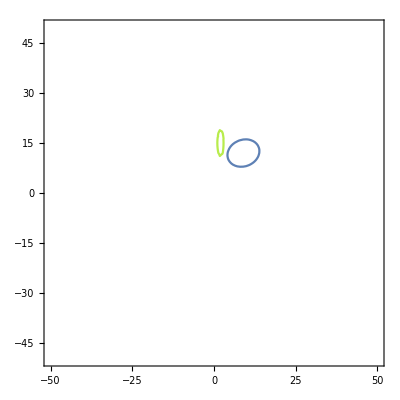

```mathematica
Show[e1Plot,e2Plot]
```

```mathematica
eTestA = ContourPlot[a11*x^2 + 2*a12*x*y+a22*y^2  + 2*a13*x + 2*a23*y + a33==0,{x,-50,50},{y,-50,50}];
```

```mathematica
eTestB = ContourPlot[b11*x^2 + 2*b12*x*y+b22*y^2  + 2*b13*x + 2*b23*y + b33==0,{x,-50,50},{y,-50,50},ColorFunction->"NeonColors"];
```

```mathematica
Show[eTestA,eTestB]
```

-Graphics-

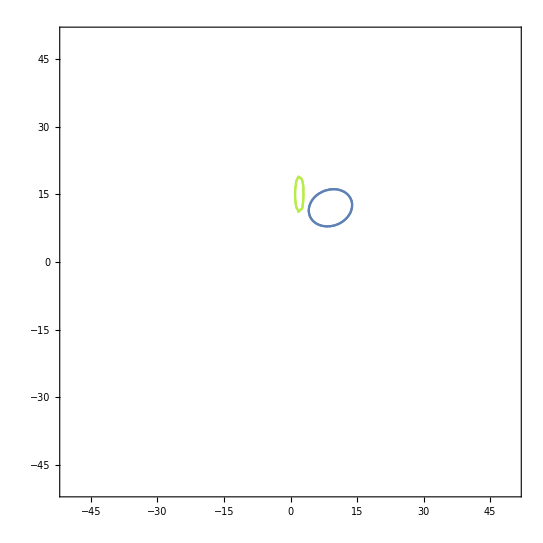

```mathematica
Show[eTestA,eTestB,e1Plot,e2Plot]
```

```mathematica
If[(a ≥ 0 &&  (-3*b+a^2)>0 && (3*a*c + b*a^2 - 4*b^2) < 0 && (-27c^2 + 18*c*a*b + a^2*b^2 - 4*a^3*c - 4*b^3) > 0 ) || (a <0 && (-3*b+a^2)>0 && (-27c^2 + 18*c*a*b + a^2*b^2 - 4*a^3*c - 4*b^3) > 0 ),"Ellipses are separated!","Ellipses overlap!"]
```

Ellipses are separated!